Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

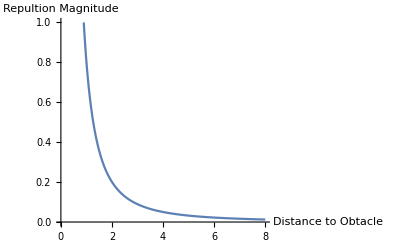

1leader-2Obstacles-Repultion Function.JPG

```mathematica
Clear["Global`*"]
SetDirectory@NotebookDirectory[];
ClearSystemCache[];
$HistoryLength=0; 

(* Graphical Output Parameters *)
PLxmn=0; PLxmx=40 ;    (* Plotrange {Xmin,Xmax} *)
PLymn= -5;PLymx= 20;     (* Plotrange {Xmin,Xmax} *)
AXx=0;AXy=20 ;              (* Axis Origin {X,Y} *)
DiskSize= 0.02;                        (* Size of Agents *)

(*=====Section 1: Swarm Definition=====*)

(*Number of Elements Per Side+Fictitious*)
n=11;

(*Leaders' Settings*)

nl=1;                    (*Number of leaders*)
ldx={2,0};       (*Leaders' X-Coordinates*)
ldy={10,0};     (*Leaders' Y-Coordinates*)


(*=====Goal Setting=====*)
gx=35;
gy=9; 
Speed= 0.05;          (* Speed *)

disx={0.0,0.0,0.0};
disy={0.0,0.0,0.0};

GoalZone=Graphics[{Green,Disk[{gx,gy},0.5]}];     (*Goal Graphics*)

(*==== Obstacle Settings=====*)

Nob= 1; (*Number of Obstacles *)
Tx={15,25,16,16};
Ty={1,9,3,14} ;
Tp=-2;                 (*Target Power of Repultion*)
Tw=0.8;                   (*Weight Factor of Repulsion*)
eps=Speed;         (*epsilon: Min Effect of Obstacle on Swarm Particles *)
Zones=Table[0,{i,Nob}];



(* Repulsion Function Y=Tw*X^Tp & Tp<0 *)
Sz1=Solve[Tw*(Sz^Tp)==eps && Sz>0,Sz]//N;  (* Sz: Safe Zone Margin *)
Sz2=Sz/.Sz1;
Plot[Tw*(Sz^Tp),{Sz,0,Sz2[[1]]*2},AxesLabel->{"Distance to Obtacle","Repultion Magnitude"}]
Export["1leader-2Obstacles-Repultion Function.JPG",%]

For[ ob=1,ob≤Nob,ob++,

(* Obstacle Effective Zone Graphics*)
Zones[[ob]]=Graphics[{Red,Dashed,Circle[{Tx[[ob]],Ty[[ob]]},Sz2[[1]]],Red,Disk[{Tx[[ob]],Ty[[ob]]},0.5]}];
];

(* Poisson Coefficient*)
pc=1;

(*Definition of the matrices of coordinate in C_0*)
x=Table[x=j,{i,n},{j,n}];
y=Table[y=n-i,{i,n},{j,n}];

xl=Table[xl=j,{i,n},{j,n},{k,nl}];
yl=Table[yl=n-i,{i,n},{j,n},{k,nl}];

x//MatrixForm;
y//MatrixForm;

xl//MatrixForm;
yl//MatrixForm;

(*Matrici per calcolo pesi*)
w=Table[1,{n},{n},{nl}];
pl=Table[1,{n},{n},{nl}];
d=Table[0,{n},{n},{nl}];


(*number of iterations*)
timestop=2000;
Trest=timestop; (* Movement Steps*)

(* Energy Arrays *)
energy=Table[0,{i,timestop}];

(*Cicle to iterate my external action*)
snapshot=Table[0,{i,timestop}];
TableTime1=Table[{x[[i,j]],y[[i,j]]},{i,2,n-1},{j,2,n-1}];

(* First Frame *)
snapshot[[1]]=Show[ListPlot[Table[{x[[i,j]],y[[i,j]]},{i,2,n-1},{j,2,n-1}],PlotMarkers->{Graphics[{Blue,Disk[]}],DiskSize} ,PlotStyle->Blue,PlotRange->{{PLxmn,PLxmx},{PLymn,PLymx}},AspectRatio->Automatic,AxesOrigin->{AXx,AXy},ImageSize->Large],Zones,GoalZone];


(*===Section2: Processing=======*)

(*2.1:Time Step Loop*)

For[step=1,step<timestop,step++,
ClearSystemCache[];
aa=xl;
bb=yl;
 
(* ==== Movement Scenarios by Time ====*)


(*==Obstacle on leader==*)

(* Direction & Distance Calculation from Obstacles *) 

LobRepulseX=Table[0,{i,Nob}];
LobRepulseY=Table[0,{i,Nob}];


(*Phase 1: Movement *)
If[step<Trest, Sp=Speed];

(*Phase 2: Rest *)
If[Trest≤step<timestop, Sp=0];


(*At this point I can introduce the external perturbation on the leader(s)*)

For[ld=1,ld≤nl,ld++,
il=ldx[[ld]];
jl=ldy[[ld]];


For[ ob=1,ob≤Nob,ob++,

Lobdis=EuclideanDistance[{Tx[[ob]],Ty[[ob]]},{xl[[il , jl,ld]],yl[[il , jl ,ld]]}];
Lobcos=(Tx[[ob]]-xl[[il, jl,ld]])/(Lobdis);
Lobsin=(Ty[[ob]]-yl[[il , jl ,ld]])/(Lobdis);


(* Repulsion Function Y=Tw*X^Tp & Tp<0 *) 
LobRepulseX[[ob]]=Lobcos*(1.2*Tw)*(Lobdis)^Tp;
LobRepulseY[[ob]]=Lobsin*(1.2*Tw)*(Lobdis)^Tp;

];

LobTcoefX=Total[LobRepulseX];
LobTcoefY=Total[LobRepulseY];

(* Direction Module *)
Gdis=EuclideanDistance[{gx,gy},{xl[[il,jl,ld]],yl[[il,jl,ld]]}];
Gcos=(xl[[il,jl,ld]]-gx)/(Gdis);
Gsin=(yl[[il,jl,ld]]-gy)/(Gdis);

(* Attraction Function Y=Sp , contant speed*)

disx[[ld]]=-Sp*Gcos;  (* X-component Speed *)
disy[[ld]]=-Sp*Gsin ; (* Y-Component Speed *)

If[step≤timestop,
xl[[il,jl,ld]]=xl[[il,jl,ld]]+disx[[ld]]-LobTcoefX ;
yl[[il,jl,ld]]=yl[[il,jl,ld]]+disy[[ld]]-LobTcoefY ;
xl[[il,jl,ld]]=xl[[il,jl,ld]]; (* comment kon and see what happens. why is this here? *)
yl[[il,jl,ld]]=yl[[il,jl,ld]];
];

p=Max[(il-2),(jl-2),n-il-1,n-jl-1];

peso=1./8.;

(*Other auxiliary matrix for calculation*)
xd=Table[xd=0,{i,n},{j,n}];
yd=Table[yd=0,{n},{n}];

For[s=1,s≤p,s++,
For[l=-s,l≤s,l++, 
For[t=-s,t≤s,t++,
If[((il+l)≤1 ∨(il+l)≥n),Continue,
 If[((jl+t)≤1 ∨(jl+t)≥n),Continue,
  If[(Abs[l]==s∨Abs[t]==s),

(* Direction & Distance Calculation from Obstacles *) 

RepulseX=Table[0,{i,Nob}];
RepulseY=Table[0,{i,Nob}];

For[ ob=1,ob≤Nob,ob++,

Tdis=EuclideanDistance[{Tx[[ob]],Ty[[ob]]},{xl[[il+l , jl+t ,ld]],yl[[il+l , jl+t ,ld]]}];
cos=(Tx[[ob]]-xl[[il+l , jl+t ,ld]])/(Tdis);
sin=(Ty[[ob]]-yl[[il+l , jl+t ,ld]])/(Tdis);


(* Repulsion Function Y=Tw*X^Tp & Tp<0 *) 
RepulseX[[ob]]=cos*Tw*(Tdis)^Tp;
RepulseY[[ob]]=sin*Tw*(Tdis)^Tp;

];

TcoefX=Total[RepulseX];
TcoefY=Total[RepulseY];


(*Main Algorithm*)

xd[[il+l,jl+t]]=peso*(
  xl[[il+l-1,jl+t-1,ld]]+
xl[[il+l-1,jl+t,ld]]+
xl[[il+l-1,jl+t+1,ld]]+
xl[[il+l,jl+t+1,ld]]+
xl[[il+l+1,jl+t+1,ld]]+
xl[[il+l+1,jl+t,ld]]+
xl[[il+l+1,jl+t-1,ld]]+
xl[[il+l,jl+t-1,ld]])-TcoefX;

yd[[il+l,jl+t]]=peso*(
  yl[[il+l-1,jl+t-1,ld]]+
yl[[il+l-1,jl+t,ld]]+
yl[[il+l-1,jl+t+1,ld]]+
yl[[il+l,jl+t+1,ld]]+
yl[[il+l+1,jl+t+1,ld]]+
yl[[il+l+1,jl+t,ld]]+
yl[[il+l+1,jl+t-1,ld]]+
yl[[il+l,jl+t-1,ld]])-TcoefY;
]
]
]
]
];
For[l=-s,l≤s,l++, 
For[t=-s,t≤s,t++,
If[((il+l)≤1 ∨(il+l)≥n),Continue,
 If[((jl+t)≤1 ∨(jl+t)≥n),Continue,
  If[(Abs[l]==s∨Abs[t]==s), 
xl[[il+l,jl+t,ld]]=xd[[il+l,jl+t]];
yl[[il+l,jl+t,ld]]=yd[[il+l,jl+t]];
]
]
]
]
]
];

(*Repostioning the leader*)
For[k=1,k≤nl,k++,
For[h=1,h≤nl,h++,
xl[[ldx[[h]],ldy[[h]],k]]=xl[[ldx[[h]],ldy[[h]],h]];
yl[[ldx[[h]],ldy[[h]],k]]=yl[[ldx[[h]],ldy[[h]],h]];
]
];

(*======Rearrangement of the ficticious boundary======*)

(*LATO (i,1)*)
For[i=2,i<n,i++,
mb=0; a=0; b=0; c=0; x1=0; x2=0; y1=0; y2=0;r=0;
r=1-pc*(EuclideanDistance[{ xl[[i+1,1,ld]],yl[[i+1,1,ld]]},{xl[[i,1,ld]],yl[[i,1,ld]]}]+EuclideanDistance[{ xl[[i-1,1,ld]],yl[[i-1,1,ld]]},{xl[[i,1,ld]],yl[[i,1,ld]]}]-2)/2;
If[yl[[i,2,ld]]==yl[[i,3,ld]],
yl[[i,1,ld]]=yl[[i,2,ld]];
If[xl[[i,2,ld]]-xl[[i,3,ld]]≥0,
xl[[i,1,ld]]=xl[[i,2,ld]]+r,
xl[[i,1,ld]]=xl[[i,2,ld]]-r
],

If[xl[[i,2,ld]]==xl[[i,3,ld]],
xl[[i,1,ld]]=xl[[i,2,ld]];
If[yl[[i,2,ld]]-yl[[i,3,ld]]≥0,
yl[[i,1,ld]]=yl[[i,2,ld]]+r,
yl[[i,1,ld]]=yl[[i,2,ld]]-r
],

mb=(yl[[i,2,ld]]-yl[[i,3,ld]])/(xl[[i,2,ld]]-xl[[i,3,ld]]);
a=(1+mb^2);

x1=xl[[i,2,ld]]-(r/Sqrt[a]);
x2=xl[[i,2,ld]]+(r/Sqrt[a]);

y1=mb*(x1-xl[[i,2,ld]])+yl[[i,2,ld]];
y2=mb*(x2-xl[[i,2,ld]])+yl[[i,2,ld]];

If[yl[[i,2,ld]]-yl[[i,3,ld]]<0,
yl[[i,1,ld]]=Min[y1, y2],
yl[[i,1,ld]]=Max[y1, y2]
];
xl[[i,1,ld]]=xl[[i,2,ld]]+((yl[[i,1,ld]]-yl[[i,2,ld]])/mb);
]
]
];

(*LATO (1,i)*)
For[i=2,i<n,i++,
mb=0; a=0; b=0; c=0; x1=0; x2=0; y1=0; y2=0;r=0;
r=1-pc*(EuclideanDistance[{ xl[[1,i+1,ld]],yl[[1,i+1,ld]]},{xl[[1,i,ld]],yl[[1,i,ld]]}]+EuclideanDistance[{ xl[[1,i-1,ld]],yl[[1,i-1,ld]]},{xl[[1,i,ld]],yl[[1,i,ld]]}]-2)/2;
If[yl[[2,i,ld]]==yl[[3,i,ld]],
yl[[1,i,ld]]=yl[[2,i,ld]];
If[xl[[2,i,ld]]-xl[[3,i,ld]]≥0,
xl[[1,i,ld]]=xl[[2,i,ld]]+r,
xl[[1,i,ld]]=xl[[2,i,ld]]-r
],
If[xl[[2,i,ld]]==xl[[3,i,ld]],
xl[[1,i,ld]]=xl[[2,i,ld]];
If[yl[[2,i,ld]]-yl[[3,i,ld]]≥0,
yl[[1,i,ld]]=yl[[2,i,ld]]+r,
yl[[1,i,ld]]=yl[[2,i,ld]]-r
],
mb=(yl[[2,i,ld]]-yl[[3,i,ld]])/(xl[[2,i,ld]]-xl[[3,i,ld]]);
a=(1+mb^2);

x1=xl[[2,i,ld]]-(r/Sqrt[a]);
x2=xl[[2,i,ld]]+(r/Sqrt[a]);

y1=mb*(x1-xl[[2,i,ld]])+yl[[2,i,ld]];
y2=mb*(x2-xl[[2,i,ld]])+yl[[2,i,ld]];

If[yl[[2,i,ld]]-yl[[3,i,ld]]<0,
yl[[1,i,ld]]=Min[y1, y2],
yl[[1,i,ld]]=Max[y1, y2]
];
xl[[1,i,ld]]=xl[[2,i,ld]]+((yl[[1,i,ld]]-yl[[2,i,ld]])/mb);
]
]
];

(*Lato(n,i)*)
For[i=2,i<n,i++,
mb=0; a=0; b=0; c=0; x1=0; x2=0; y1=0; y2=0;r=0;
r=1-pc*(EuclideanDistance[{ xl[[n,i+1,ld]],yl[[n,i+1,ld]]},{xl[[n,i,ld]],yl[[n,i,ld]]}]+EuclideanDistance[{ xl[[n,i-1,ld]],yl[[n,i-1,ld]]},{xl[[n,i,ld]],yl[[n,i,ld]]}]-2)/2;
If[yl[[n-1,i,ld]]==yl[[n-2,i,ld]],
yl[[n,i,ld]]=yl[[n-1,i,ld]];
If[xl[[n-1,i,ld]]-xl[[n-2,i,ld]]≥0,
xl[[n,i,ld]]=xl[[n-1,i,ld]]+r,
xl[[n,i,ld]]=xl[[n-1,i,ld]]-r
],
If[xl[[n-1,i,ld]]==xl[[n-2,i,ld]],
xl[[n,i,ld]]=xl[[n-1,i,ld]];
If[yl[[n-1,i,ld]]-yl[[n-2,i,ld]]≥0,
yl[[n,i,ld]]=yl[[n-1,i,ld]]+r,
yl[[n,i,ld]]=yl[[n-1,i,ld]]-r
],
mb=(yl[[n-1,i,ld]]-yl[[n-2,i,ld]])/(xl[[n-1,i,ld]]-xl[[n-2,i,ld]]);
a=(1+mb^2);

x1=xl[[n-1,i,ld]]-(r/Sqrt[a]);
x2=xl[[n-1,i,ld]]+(r/Sqrt[a]);

y1=mb*(x1-xl[[n-1,i,ld]])+yl[[n-1,i,ld]];
y2=mb*(x2-xl[[n-1,i,ld]])+yl[[n-1,i,ld]];

If[yl[[n-1,i,ld]]-yl[[n-2,i,ld]]<0,
yl[[n,i,ld]]=Min[y1, y2],
yl[[n,i,ld]]=Max[y1, y2]
];
xl[[n,i,ld]]=xl[[n-1,i,ld]]+((yl[[n,i,ld]]-yl[[n-1,i,ld]])/mb);
]
]
];

(*LATO(i,n)*)
For[i=2,i<n,i++,
mb=0; a=0; b=0; c=0; x1=0; x2=0; y1=0; y2=0;r=0;
r=1-pc*(EuclideanDistance[{ xl[[i+1,n,ld]],yl[[i+1,n,ld]]},{xl[[i,n,ld]],yl[[i,n,ld]]}]+EuclideanDistance[{ xl[[i-1,n,ld]],yl[[i-1,n,ld]]},{xl[[i,n,ld]],yl[[i,n,ld]]}]-2)/2;
If[yl[[i,n-1,ld]]==yl[[i,n-2,ld]],
yl[[i,n,ld]]=yl[[i,n-1,ld]];
If[xl[[i,n-1,ld]]-xl[[i,n-2,ld]]≥0,
xl[[i,n,ld]]=xl[[i,n-1,ld]]+r,
xl[[i,n,ld]]=xl[[i,n-1,ld]]-r
],
If[xl[[i,n-1,ld]]==xl[[i,n-2,ld]],
xl[[i,n,ld]]=xl[[i,n-1,ld]];
If[yl[[i,n-1,ld]]-yl[[i,n-2,ld]]≥0,
yl[[i,n,ld]]=yl[[i,n-1,ld]]+r,
yl[[i,n,ld]]=yl[[i,n-1,ld]]-r
],
mb=(yl[[i,n-1,ld]]-yl[[i,n-2,ld]])/(xl[[i,n-1,ld]]-xl[[i,n-2,ld]]);
a=(1+mb^2);

x1=xl[[i,n-1,ld]]-(r/Sqrt[a]);
x2=xl[[i,n-1,ld]]+(r/Sqrt[a]);

y1=mb*(x1-xl[[i,n-1,ld]])+yl[[i,n-1,ld]];
y2=mb*(x2-xl[[i,n-1,ld]])+yl[[i,n-1,ld]];

If[yl[[i,n-1,ld]]-yl[[i,n-2,ld]]<0,
yl[[i,n,ld]]=Min[y1, y2],
yl[[i,n,ld]]=Max[y1, y2]
];
xl[[i,n,ld]]=xl[[i,n-1,ld]]+((yl[[i,n,ld]]-yl[[i,n-1,ld]])/mb);
]
]
];

(*VERTICE (1,1)*)
mb=0; a=0; b=0; c=0; x1=0; x2=0; y1=0; y2=0;

If[yl[[2,2,ld]]==yl[[3,3,ld]],
yl[[1,1,ld]]=yl[[2,2,ld]];
If[xl[[2,2,ld]]-xl[[3,3,ld]]≥0,
xl[[1,1,ld]]=xl[[2,2,ld]]+Sqrt[2],
xl[[1,1,ld]]=xl[[2,2,ld]]-Sqrt[2]
],
If[xl[[2,2,ld]]==xl[[3,3,ld]],
xl[[1,1,ld]]=xl[[2,2,ld]];
If[yl[[2,2,ld]]-yl[[3,3,ld]]≥0,
yl[[1,1,ld]]=yl[[2,2,ld]]+Sqrt[2],
yl[[1,1,ld]]=yl[[2,2,ld]]-Sqrt[2]
],
mb=(yl[[2,2,ld]]-yl[[3,3,ld]])/(xl[[2,2,ld]]-xl[[3,3,ld]]);
a=(1+mb^2);
b=-2*(xl[[2,2,ld]]*mb^2+xl[[2,2,ld]]);
c=mb^2*xl[[2,2,ld]]^2+xl[[2,2,ld]]^2-2;

x1=xl[[2,2,ld]]-(Sqrt[2/a]);
x2=xl[[2,2,ld]]+(Sqrt[2/a]);

y1=mb*(x1-xl[[2,2,ld]])+yl[[2,2,ld]];
y2=mb*(x2-xl[[2,2,ld]])+yl[[2,2,ld]];
If[yl[[2,2,ld]]-yl[[3,3,ld]]<0,
yl[[1,1,ld]]=Min[y1, y2],
yl[[1,1,ld]]=Max[y1, y2]
];
xl[[1,1,ld]]=xl[[2,2,ld]]+((yl[[1,1,ld]]-yl[[2,2,ld]])/mb);
]
];

(*VERTICE (1,n)*)
mb=0; a=0; b=0; c=0; x1=0; x2=0; y1=0; y2=0;

If[yl[[2,n-1,ld]]==yl[[3,n-2,ld]],
yl[[1,n,ld]]=yl[[2,n-1,ld]];
If[xl[[2,n-1,ld]]-xl[[3,n-2,ld]]≥0,
xl[[1,n,ld]]=xl[[2,n-1,ld]]+Sqrt[2],
xl[[1,n,ld]]=xl[[2,n-1,ld]]-Sqrt[2]
],
If[xl[[2,n-1,ld]]==xl[[3,n-2,ld]],
xl[[1,n,ld]]=xl[[2,n-1,ld]];
If[yl[[2,n-1,ld]]-yl[[3,n-2,ld]]≥0,
yl[[1,n,ld]]=yl[[2,n-1,ld]]+Sqrt[2],
yl[[1,n,ld]]=yl[[2,n-1,ld]]-Sqrt[2]
],
mb=(yl[[2,n-1,ld]]-yl[[3,n-2,ld]])/(xl[[2,n-1,ld]]-xl[[3,n-2,ld]]);
a=(1+mb^2);

x1=xl[[2,n-1,ld]]-(Sqrt[2/a]);
x2=xl[[2,n-1,ld]]+(Sqrt[2/a]);

y1=mb*(x1-xl[[2,n-1,ld]])+yl[[2,n-1,ld]];
y2=mb*(x2-xl[[2,n-1,ld]])+yl[[2,n-1,ld]];
If[yl[[2,n-1,ld]]-yl[[3,n-2,ld]]<0,
yl[[1,n,ld]]=Min[y1, y2],
yl[[1,n,ld]]=Max[y1, y2]
];
xl[[1,n,ld]]=xl[[2,n-1,ld]]+((yl[[1,n,ld]]-yl[[2,n-1,ld]])/mb);
]
];

(*VERTICE (n,1)*)
mb=0; a=0; b=0; c=0; x1=0; x2=0; y1=0; y2=0;

If[yl[[n-1,2,ld]]==yl[[n-2,3,ld]],
yl[[n,1,ld]]=yl[[n-1,2,ld]];
If[xl[[n-1,2,ld]]-xl[[n-2,3,ld]]≥0,
xl[[n,1,ld]]=xl[[n-1,2,ld]]+Sqrt[2],
xl[[n,1,ld]]=xl[[n-1,2,ld]]-Sqrt[2]
],
If[xl[[n-1,2,ld]]==xl[[n-2,3,ld]],
xl[[n,1,ld]]=xl[[n-1,2,ld]];
If[yl[[n-1,2,ld]]-yl[[n-2,3,ld]]≥0,
yl[[n,1,ld]]=yl[[n-1,2,ld]]+Sqrt[2],
yl[[n,1,ld]]=yl[[n-1,2,ld]]-Sqrt[2]
],
mb=(yl[[n-1,2,ld]]-yl[[n-2,3,ld]])/(xl[[n-1,2,ld]]-xl[[n-2,3,ld]]);
a=(1+mb^2);
b=-2*(xl[[n-1,2,ld]]*mb^2+xl[[n-1,2,ld]]);
c=mb^2*xl[[n-1,2,ld]]^2+xl[[n-1,2,ld]]^2-2;

x1=xl[[n-1,2,ld]]-(Sqrt[2/a]);
x2=xl[[n-1,2,ld]]+(Sqrt[2/a]);

y1=mb*(x1-xl[[n-1,2,ld]])+yl[[n-1,2,ld]];
y2=mb*(x2-xl[[n-1,2,ld]])+yl[[n-1,2,ld]];

If[yl[[n-1,2,ld]]-yl[[n-2,3,ld]]<0,
yl[[n,1,ld]]=Min[y1, y2],
yl[[n,1,ld]]=Max[y1, y2]
];
xl[[n,1,ld]]=xl[[n-1,2,ld]]+((yl[[n,1,ld]]-yl[[n-1,2,ld]])/mb);
]
];

(*VERTICE (n,n)*)
mb=0; a=0; b=0; c=0; x1=0; x2=0; y1=0; y2=0;

If[yl[[n-1,n-1,ld]]==yl[[n-2,n-2,ld]],
yl[[n,n,ld]]=yl[[n-1,n-1,ld]];
If[xl[[n-1,n-1,ld]]-xl[[n-2,n-2,ld]]≥0,
xl[[n,n,ld]]=xl[[n-1,n-1,ld]]+Sqrt[2],
xl[[n,n,ld]]=xl[[n-1,n-1,ld]]-Sqrt[2]
],
If[xl[[n-1,n-1,ld]]==xl[[n-2,n-2,ld]],
xl[[n,n,ld]]=xl[[n-1,n-1,ld]];
If[yl[[n-1,n-1,ld]]-yl[[n-2,n-2,ld]]≥0,
yl[[n,n,ld]]=yl[[n-1,n-1,ld]]+Sqrt[2],
yl[[n,n,ld]]=yl[[n-1,n-1,ld]]-Sqrt[2]
],
mb=(yl[[n-1,n-1,ld]]-yl[[n-2,n-2,ld]])/(xl[[n-1,n-1,ld]]-xl[[n-2,n-2,ld]]);
a=(1+mb^2);

x1=xl[[n-1,n-1,ld]]-(Sqrt[2/a]);
x2=xl[[n-1,n-1,ld]]+(Sqrt[2/a]);

y1=mb*(x1-xl[[n-1,n-1,ld]])+yl[[n-1,n-1,ld]];
y2=mb*(x2-xl[[n-1,n-1,ld]])+yl[[n-1,n-1,ld]];

If[yl[[n-1,n-1,ld]]-yl[[n-2,n-2,ld]]<0,
yl[[n,n,ld]]=Min[y1, y2],
yl[[n,n,ld]]=Max[y1, y2]
];
xl[[n,n,ld]]=xl[[n-1,n-1,ld]]+((yl[[n,n,ld]]-yl[[n-1,n-1,ld]])/mb);
]
]
];

(*Weighted Sum of Leaders' Contribution*)
For[l=1,l≤n,l++,
For[t=1,t≤n,t++,
x[[l,t]]=x[[l,t]]+Sum[w[[l,t,i]]*(xl[[l,t,i]]-aa[[l,t,i]]),{i,1,nl}];
y[[l,t]]=y[[l,t]]+Sum[w[[l,t,i]]*(yl[[l,t,i]]-bb[[l,t,i]]),{i,1,nl}];
]
];

(*======Energy Evaluation=========*)


For[i=2,i<n-2,i++,For[j=2,j<n-2,j++,energy[[step]]=energy[[step]]+((EuclideanDistance[{x[[i,j]],y[[i,j]]},{x[[i,j+1]],y[[i,j+1]]}]-1))^2+((EuclideanDistance[{x[[i,j]],y[[i,j]]},{x[[i+1,j+1]],y[[i+1,j+1]]}]-Sqrt[2])/Sqrt[2])^2+((EuclideanDistance[{x[[i,j]],y[[i,j]]},{x[[i+1,j]],y[[i+1,j]]}]-1))^2
];
];

For[i=3,i<n,i++,For[j=2,j<n,j++,energy[[step]]=energy[[step]]+((EuclideanDistance[{x[[i,j]],y[[i,j]]},{x[[i+1,j-1]],y[[i+1,j-1]]}]-Sqrt[2])/Sqrt[2])^2;
];
];

For[i=2,i<n-1,i++,energy[[step]]=energy[[step]]+((EuclideanDistance[{x[[i,n-1]],y[[i,n-1]]},{x[[i+1,n-1]],y[[i+1,n-1]]}]-1))^2;
];

For[i=2,i<n-1,i++,energy[[step]]=energy[[step]]+((EuclideanDistance[{x[[n-1,i]],y[[n-1,i]]},{x[[n-1,i+1]],y[[n-1,i+1]]}]-1))^2;

];


(*===================Graphic Visualization=================*)

(*
snapshot[[step+1]]=Show[ListPlot[Table[{x[[i,j]],y[[i,j]]},{i,2,n-1},{j,2,n-1}],PlotMarkers->{Graphics[{Blue,Disk[]}],0.01},PlotStyle->Blue,PlotRange->{{0,50},{0,50}},AspectRatio->Automatic,Epilog->{Red,PointSize->.01,Point[{xl[[il,jl,1]],yl[[il,jl,1]]}]},ImageSize->Large] ,Zones, GoalZone];
*)






(*======Image String Export=====*)


Export["F"<>ToString[step]<>".JPG",{Show[ListPlot[Table[{x[[i,j]],y[[i,j]]},{i,2,n-1},{j,2,n-1}],PlotMarkers->{Graphics[{Blue,Disk[]}],DiskSize} ,PlotStyle->Blue,PlotRange->{{PLxmn,PLxmx},{PLymn,PLymx}},AspectRatio->Automatic,AxesOrigin->{AXx,AXy},Epilog->{Cyan ,PointSize->DiskSize,Point[{xl[[il,jl,1]],yl[[il,jl,1]]}]},ImageSize->Large],GoalZone,Zones]}]

ClearSystemCache[];

]//AbsoluteTiming

(*
(*=========Video Export=========*)
Export["1Leader-2Obstacle_ParallelObstacles2.avi",snapshot]//AbsoluteTiming
*)




ClearSystemCache[];

(* 
ListAnimate[snapshot,1,ImageSize->Large,FrameLabel->{{"y","Tp=-2"},{"x","Repultion Test1: Target{12,5}"}}]
 *)

ClearSystemCache[];
```

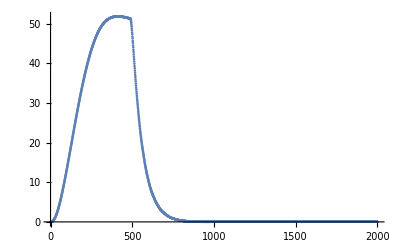

1Leader-2Obstacle_ParallelObstacles_Energy2.JPG

```mathematica
ListPlot[energy,AxesLabel->Automatic]
Export["1Leader-2Obstacle_ParallelObstacles_Energy2.JPG",%]
```